# Dimension

Can the same dimension be read from counting vertices and from covering them with larger graph balls? We compare these measurements across a range of graph distances. The drawing supplies no measurement.

## Growth and scale

Write B_s(c)=={v:d(c,v)≤s} and V(s)==|B_s(c)|. A power law V(s)∼C s^d gives V(λs)/V(s)→λ^d at each fixed λ>0. Scaling lengths by λ scales volume by λ^d. This is the scale comparison we test. A finite graph provides only a window between its individual layers and its boundary.

```mathematica
Needs[ "WolframInstitute`InfraGeometry`" ]
```

The mesh and regular tilings have reference growth dimension two. The Sierpinski triangle has three half-sized copies, giving d==log3/log2. The planar Menger carpet has eight third-sized copies, giving d==log8/log3. These are reference dimensions of the limiting constructions; the graphs below are finite approximations. The carpet uses three construction steps to keep the covering calculations practical. Three unfilled gray contours show convex envelopes of balls at roughly one third, two thirds and the full target radius. The target radius is four fifths of the graph radius, rounded down. The contours show growth in the drawing; the balls themselves are defined by graph distance.

```mathematica
SeedRandom[ 2 ];
dimensionSubstrates = Apply[
  { name, size, reference } |-> With[
    { graph = InfraSubstrate[ name, size, "KeepCoordinates" -> True ] },
    { centre = First @ GraphCenter[ graph ], radius = Floor[ 4 GraphRadius[ graph ] / 5 ] },
    <| "Name" -> name, "Graph" -> graph, "Centre" -> centre, "Radius" -> radius,
      "Reference" -> reference |> ],
  { { "SquareMeshGraph", "Large", 2 }, { "SquareTilingGraph", "Large", 2 },
    { "TriangularTilingGraph", "Large", 2 }, { "HexagonalTilingGraph", "Large", 2 },
    { "SierpinskiTriangleGraph", "Large", Log[ 3 ] / Log[ 2 ] },
    { "MengerCarpetGraph", "Medium", Log[ 8 ] / Log[ 3 ] } }, { 1 } ];
GraphicsGrid[ Partition[ Map[
  data |-> With[
    { graph = data[ "Graph" ], centre = data[ "Centre" ], radius = data[ "Radius" ] },
    { balls = Map[ r |-> Keys @ InfraMeasurement[ graph, InfraBall[ centre, r ], "VertexDensity" ],
        Floor[ radius { 1/3, 2/3, 1 } ] ] },
    Labeled[ InfraSubstrateHighlight[ graph, { centre -> StandardGray },
      Epilog -> { StandardGray, AbsoluteThickness[ 1.5 ], Map[
        vertices |-> MeshPrimitives[
          ConvexHullMesh[ GraphEmbedding[ graph ][[ Map[ v |-> VertexIndex[ graph, v ], vertices ] ]] ], 1 ],
        balls ] } ,
      "ThicknessRange" -> { 1.25, 5 } ], data[ "Name" ] ] ],
  dimensionSubstrates ], 3 ], ImageSize -> 1200 ]
```

-Graphics-

## Covering a region

Let N_r(T) be the least number of closed graph balls of radius r covering a target T. Their centres may lie outside T, and shortest paths are measured in the surrounding graph. FindBallCover minimizes the number of centres by default; Method -> "Greedy" gives an upper bound. BallCoverNumber returns the minimum.

Here an exact cover of B_4(c) uses balls of radius two. The target is gray. Unfilled gray contours show convex envelopes of the covering balls in the drawing, keeping their overlaps visible. The cover is computed from graph balls, not these envelopes.

```mathematica
SeedRandom[ 2 ];
With[
  { graph = InfraSubstrate[ "SquareTilingGraph", "Small", "KeepCoordinates" -> True ] },
  { target = InfraBall[ First @ GraphCenter[ graph ], 4 ], radius = 2 },
  { centres = FindBallCover[ graph, radius, target ] },
  GraphicsRow[ {
    Labeled[ InfraSubstrateHighlight[ graph, { target -> StandardGray } ,
      "ThicknessRange" -> { 1.25, 5 } ], "target" ],
    Labeled[ Show[ InfraSubstrateHighlight[ graph, { target -> StandardGray, centres -> StandardGray },
      Epilog -> { StandardGray, AbsoluteThickness[ 1.5 ], Map[
        point |-> With[
          { vertices = Keys @ InfraMeasurement[ graph, InfraBall[ point, radius ], "VertexDensity" ] },
          MeshPrimitives[ ConvexHullMesh[ GraphEmbedding[ graph ][[ Map[ v |-> VertexIndex[ graph, v ], vertices ] ]] ], 1 ] ],
        centres ] } ,
      "ThicknessRange" -> { 1.25, 5 } ] ], "minimum radius-two cover" ] }, ImageSize -> 900 ] ]
```

-Graphics-

The same construction on the six substrates uses greedy covers. The covering radius is roughly one third of the target radius.

```mathematica
SeedRandom[ 2 ];
GraphicsGrid[ Partition[ Map[
  data |-> With[
    { graph = data[ "Graph" ], centre = data[ "Centre" ], targetRadius = data[ "Radius" ] },
    { radius = Max[ 1, Floor[ targetRadius / 3 ] ], target = InfraBall[ centre, targetRadius ] },
    { centres = FindBallCover[ graph, radius, target, Method -> "Greedy" ] },
    Labeled[
      Show[ InfraSubstrateHighlight[ graph, { target -> StandardGray, centres -> StandardGray },
        Epilog -> { StandardGray, AbsoluteThickness[ 1.5 ], Map[
          point |-> With[
            { vertices = Keys @ InfraMeasurement[ graph, InfraBall[ point, radius ], "VertexDensity" ] },
            MeshPrimitives[ ConvexHullMesh[ GraphEmbedding[ graph ][[ Map[ v |-> VertexIndex[ graph, v ], vertices ] ]] ], 1 ] ],
          centres ] } ,
        "ThicknessRange" -> { 1.25, 5 } ] ],
      Row[ { data[ "Name" ], ": ", Length[ centres ], " balls, radius ", radius } ] ] ],
  dimensionSubstrates ], 3 ], ImageSize -> 1200 ]
```

-Graphics-

## Does the exponent depend on resolution?

Fix r and grow the target B_s(c). Counting a radius-zero cover is exactly counting vertices. At larger r, each covering ball replaces a bounded number of vertices. Indeed, if every radius-r ball has at most M_r vertices, then

Abs[T]/M_r≤N_r(T)≤|T|.

The left inequality counts how many vertices the covering balls contain. The right inequality places one ball at each target vertex. Therefore, on an infinite graph with this bound, log|B_s(c)|/logs→d implies log N_r(B_s(c))/logs→d. The multiplicative factor M_r disappears after dividing its logarithm by logs. This preserves the growth exponent at each fixed resolution; it does not prove that a finite graph has a power-law window.

The following profiles compare vertex counts with greedy covers of radii one and two. For a count C(s) and reference exponent d, we plot

(C(s)/s^d)/(C(s_0)/s_0^d),    s_0==4.

A horizontal profile means that the exponent d describes this measurement over the displayed window. Dividing by the first value removes the different units of the three counts. The dashed curve in the square-tiling panel is the exact lattice count 2 s^2+2s+1, normalized in the same way. It provides a control for the drift caused by individual graph layers.

```mathematica
SeedRandom[ 2 ];
dimensionProfiles = Map[
  data |-> With[
    { graph = data[ "Graph" ], centre = data[ "Centre" ], radius = data[ "Radius" ] },
    { radii = Range[ 4, radius ] },
    { regions = Map[ s |-> InfraBall[ centre, s ], radii ] },
    { counts = Prepend[
        Table[ Map[ region |-> Length @ FindBallCover[ graph, r, region, Method -> "Greedy" ], regions ], { r, 1, 2 } ],
        InfraMeasurement[ graph, regions, "CountingMeasure" ] ] },
    Join[ data, <| "GrowthRadii" -> radii, "GrowthCounts" -> counts |> ] ],
  dimensionSubstrates ];
GraphicsGrid[ Partition[ Map[
  data |-> With[
    { radii = data[ "GrowthRadii" ], dimension = data[ "Reference" ], square = data[ "Name" ] === "SquareTilingGraph" },
    { profiles = Map[ counts |-> counts / radii^dimension, data[ "GrowthCounts" ] ] },
    { compared = If[ square, Append[ profiles, 2 + 2 / radii + 1 / radii^2 ], profiles ] },
    ListLinePlot[ Map[ profile |-> Transpose[ { radii, profile / First[ profile ] } ], compared ],
      PlotLabel -> data[ "Name" ],
      PlotLegends -> If[ square, { "vertices", "radius 1", "radius 2", "exact lattice" }, { "vertices", "radius 1", "radius 2" } ],
      PlotStyle -> { StandardBlue, StandardOrange, StandardGreen, Directive[ StandardGray, Dashed ] },
      AxesLabel -> { "s", "normalized count" }, GridLines -> { None, { 1 } }, PlotRange -> All ] ],
  dimensionProfiles ], 3 ], ImageSize -> 1200 ]
```

-Graphics-

Drift from the horizontal line shows how the finite profiles differ from a single power law. On the square lattice, V(s)/s^2==2+2/s+1/s^2 explains such drift even though the leading growth dimension is exactly two. The measured vertex profile coincides with this dashed control before the finite graph truncates the balls. Integer cover counts can produce steps, and the self-similar examples can oscillate with scale. The available scale windows differ between substrates. The greedy algorithm uses at most one ball per target vertex, so its counts satisfy the same bounds with M_r at fixed r. Those bounds preserve an asymptotic exponent but do not control the fitting error over this finite window.

## Changing the covering radius

Now fix T==B_ρ(c) and vary r. For a homogeneous d-dimensional region one expects N_r(T) to have order (ρ/r)^d when 1≪r≪ρ. We therefore plot the greedy count multiplied by r^d, again divided by its first value. The graph may be too small to provide a broad interval satisfying both inequalities.

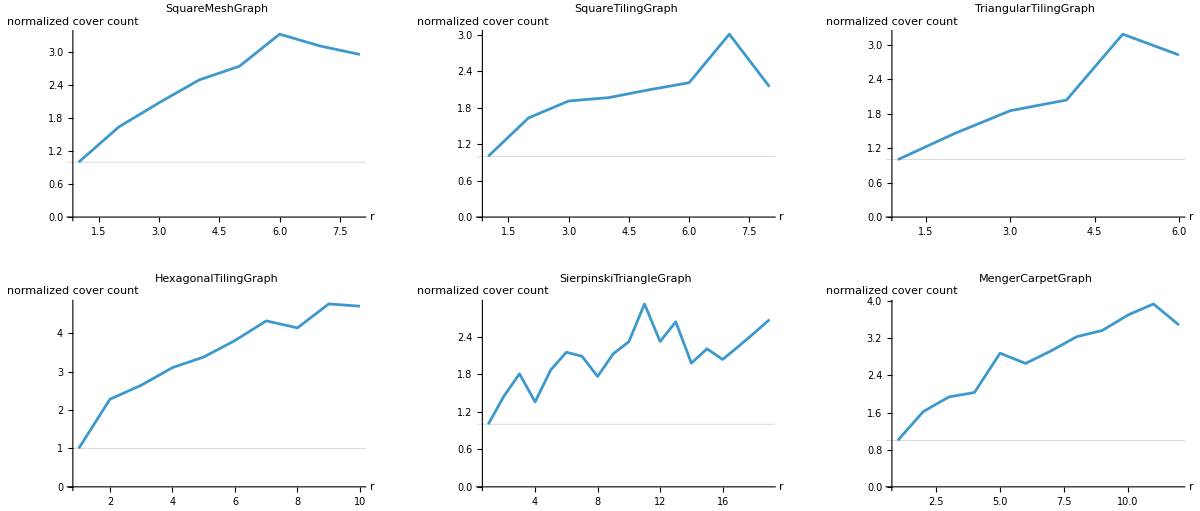

```mathematica
GraphicsGrid[ Partition[ Map[
  data |-> With[
    { graph = data[ "Graph" ], target = InfraBall[ data[ "Centre" ], data[ "Radius" ] ],
      radii = Range[ Floor[ data[ "Radius" ] / 2 ] ], dimension = data[ "Reference" ] },
    { counts = Map[ r |-> Length @ FindBallCover[ graph, r, target, Method -> "Greedy" ], radii ] },
    { profile = counts radii^dimension },
    ListLinePlot[ Transpose[ { radii, profile / First[ profile ] } ],
      PlotLabel -> data[ "Name" ], AxesLabel -> { "r", "normalized cover count" },
      GridLines -> { None, { 1 } }, PlotRange -> All ] ],
  dimensionSubstrates ], 3 ], ImageSize -> 1200 ]
```

Here the cover size itself changes with resolution, so the fixed-r bound above does not establish the expected exponent. The lattice correction, ball shape, target boundary and greedy overhead all affect this plot. No universal half-step correction to the covering radius exists.

## What dimension does not determine

The square tiling and the plane mesh can have the same volume-growth exponent while having different ball shapes. The single-scale quantity log_2 N_r(B_(2r)(c)) also includes the overlap needed to cover a ball, so it need not match that exponent. A greedy cover provides only an upper bound for this quantity.

Ball hulls give another shape-sensitive test. InfraBallHull intersects all graph balls containing the chosen points. In Euclidean space, the corresponding intersection is their convex hull. The gallery compares two tilings, a planar mesh, a sphere mesh, a spatial mesh and a Sierpinski graph. Each pair is chosen along a shortest path, and a third point is chosen at roughly the same distance from both endpoints. The pair hull is dark blue; additional vertices in the triple hull are pale blue; the three points are red. All choices use graph distance and the graphs retain their default layouts.

```mathematica
GraphicsGrid[ Partition[ Table[
  With[
    { graph = BlockRandom[ InfraSubstrate[ name, "Large" ], RandomSeeding -> 2 ] },
    { vertices = VertexList[ graph ], distances = GraphDistanceMatrix[ graph ],
      centre = First @ GraphCenter[ graph ], spread = Floor[ GraphRadius[ graph ] / 3 ] },
    { centreIndex = VertexIndex[ graph, centre ] },
    { endpoint = vertices[[ First @ Ordering[ distances[[ centreIndex ]], -1 ] ]] },
    { path = FindShortestPath[ graph, centre, endpoint ] },
    { pair = Map[ v |-> VertexIndex[ graph, v ], path[[ { 1, spread + 1 } ]] ] },
    { candidates = Complement[ Range[ Length[ vertices ] ], pair ] },
    { third = First @ MinimalBy[ candidates, index |-> Total[ Abs[ distances[[ pair, index ]] - spread ] ] ] },
    { seeds = vertices[[ Append[ pair, third ] ]] },
    { hulls = Table[ Keys @ InfraMeasurement[ graph, InfraBallHull[ Take[ seeds, k ] ], "VertexDensity" ], { k, 2, 3 } ] },
    Labeled[ InfraSubstrateHighlight[ graph,
      { Complement[ hulls[[ 2 ]], Join[ hulls[[ 1 ]], seeds ] ] -> Lighter[ StandardBlue, 0.6 ],
        Complement[ hulls[[ 1 ]], seeds ] -> StandardBlue,
        seeds -> { StandardRed, AbsolutePointSize[ 7 ] } } ,
      "ThicknessRange" -> { 1.25, 5 } ], name ] ],
  { name, { "SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph",
    "SphereMeshGraph", "CubeMeshGraph", "SierpinskiTriangleGraph" } } ], 3 ], ImageSize -> 1200 ]
```

-Graphics-

These are finite hulls, whose size depends on the surrounding graph and its available enclosing balls. A pair can already have a substantial hull. The square-tiling example below chooses a pair with a unique shortest path, shown in green. Its blue ball hull extends beyond that path. We then add a third point outside the path but inside the hull. The hull remains unchanged: every ball containing the original pair already contains the third point. More generally, if H(S) is the intersection of all balls containing S and q∈H(S), then H(S∪{q})==H(S).

```mathematica
With[
  { graph = BlockRandom[ InfraSubstrate[ "SquareTilingGraph", "Large" ], RandomSeeding -> 2 ] },
  { centre = First @ GraphCenter[ graph ], separation = 2 Floor[ GraphRadius[ graph ] / 4 ] },
  { shell = Keys @ InfraMeasurement[ graph, InfraShell[ centre, separation ], "VertexDensity" ] },
  { endpoint = SelectFirst[ shell,
      v |-> InfraMeasurement[ graph, InfraSegment[ centre, v ], "Cardinality" ] === 1 ] },
  { pair = { centre, endpoint }, distances = { GraphDistance[ graph, centre ], GraphDistance[ graph, endpoint ] } },
  { pairHull = Keys @ InfraMeasurement[ graph, InfraBallHull[ pair ], "VertexDensity" ],
    interval = Keys @ InfraMeasurement[ graph, InfraSegment[ centre, endpoint ], "VertexDensity" ] },
  { third = First @ MaximalBy[ Complement[ pairHull, interval ],
      v |-> Min[ distances[[ All, VertexIndex[ graph, v ] ]] ] ] },
  { seeds = Append[ pair, third ] },
  GraphicsGrid[ { Table[ With[
    { points = Take[ seeds, k ] },
    { hull = Keys @ InfraMeasurement[ graph, InfraBallHull[ points ], "VertexDensity" ] },
    Labeled[ InfraSubstrateHighlight[ graph,
      { Complement[ hull, Join[ interval, points ] ] -> StandardBlue,
        InfraSegment[ centre, endpoint ] -> StandardGreen, points -> { StandardRed, AbsolutePointSize[ 7 ] } } ,
      "ThicknessRange" -> { 1.25, 5 } ],
      If[ k === 2, "two points: hull beyond the path", "third point: same hull" ] ] ], { k, 2, 3 } ] }, ImageSize -> 1000 ] ]
```

-Graphics-

The taxicab-plane calculation explains this filled hull. In the taxicab plane, the ball hull of (-a,0) and (a,0) is |x|+|y|≤a, for a>0. For a centre z, the least enclosing radius is a+∥z∥_1, so the triangle inequality places the diamond in every enclosing ball. The radius-a ball at the origin gives the reverse inclusion. Thus this pair spans an area even when volume growth has dimension two.

## Related readings

Volume Measurement proves a rescaled lattice-volume limit and compares counting with the interior measure.

LogDifferenceQuotients reads successive log-log slopes of a volume profile sampled at radii one, two, and so on.

VolumeGrowthObservables and DimensionCurvatureFit fit dimension and curvature over a selected scale window.

MetricDimension is a different graph invariant: the size of a resolving set whose distances distinguish the vertices.

Related Guides

InfraTopologypaclet:WolframInstitute/InfraGeometry/guide/InfraTopology ▪ RiemannianInfrageometrypaclet:WolframInstitute/InfraGeometry/guide/RiemannianInfrageometry

Related Tech Notes

VolumeMeasurementTutorialpaclet:WolframInstitute/InfraGeometry/tutorial/VolumeMeasurementTutorial

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/DimensionTutorial

### Keywords

dimension

volume growth

ball cover

box dimension

doubling

Sierpinski triangle

Menger carpet